```mathematica
γ0 = {{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}};
γ1 = {{0, 0, 0, 1}, {0, 0, 1, 0}, {0, -1, 0, 0}, {-1, 0, 0, 0}};
γ2 = {{0, 0, 0, -ⅈ}, {0, 0, ⅈ, 0}, {0, ⅈ, 0, 0}, {-ⅈ, 0, 0, 0}};
γ3 = {{0, 0, 1, 0}, {0, 0, 0, -1}, {-1, 0, 0, 0}, {0, 1, 0, 0}};
γI = {{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}};

γs = {γ0,γ1, γ2, γ3};
γ[i_] := γs[[i + 1]]

p = {E, 0, 0, E};
pP = {E, 0, 0, -E};
k = {E, 0, E*Sin[θ], E*Cos[θ]};
kP = {E, 0, -E*Sin[θ], -E*Cos[θ]};

pSlash = p.η.γs;
pPSlash = pP.η.γs;
kSlash = k.η.γs;
kPSlash = kP.η.γs;

η = {{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}};
g[μ_, ν_] := η[[μ + 1, ν + 1]]
```

-0.0+0.(8 ⅇ^2 Sin[θ]^2)+2 0.(-4 ⅇ^2 Sin[2 θ])+(8 ⅇ^2).(8 ⅇ^2)+(8 ⅇ^2).(8 ⅇ^2 Cos[θ]^2)

```mathematica
(*Checking identities*)
Table[Tr[γ[μ].γ[ν]], {μ, 0, 3}, {ν, 0, 3}] // MatrixForm
Table[Tr[γ[μ].γ[ν].γ[1]], {μ, 0, 3}, {ν, 0, 3}] // MatrixForm
```

(4 | 0 | 0 | 0
0 | -4 | 0 | 0
0 | 0 | -4 | 0
0 | 0 | 0 | -4)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(*Check a calculation from the notes: Notes 9, pages 2 and 6, muon scattering amplitude, limit of zero muon mass*)
p = {EE, 0, 0, EE};
pP = {EE, 0, 0, -EE};
k = {EE, 0, Sqrt[EE^2 - mμ^2]*Sin[θ], Sqrt[EE^2 - mμ^2]*Cos[θ]};
kP = {EE, 0, -Sqrt[EE^2 - mμ^2]*Sin[θ], -Sqrt[EE^2 - mμ^2]*Cos[θ]};

pSlash = p.η.γs;
pPSlash = pP.η.γs;
kSlash = k.η.γs;
kPSlash = kP.η.γs;

(* This is (2) in the notes *)
e^4/(4((p + pP).η.(p + pP))^2)Sum[Tr[pPSlash.γ[μ].pSlash.γ[ν]]*g[μ,μ]*g[ν,ν]*Tr[(kSlash + mμ*γI).γ[μ].(kPSlash - mμ*γI).γ[ν]], {μ, 0, 3}, {ν, 0, 3}];
(* THIS MATCHES (5) *)
Series[%, {mμ, 0, 3}] // FullSimplify
```

e^4 (1+Cos[θ]^2)+(e^4 Sin[θ]^2 mμ^2)/EE^2+O[mμ]^4

### Bhabha scattering

```mathematica
p = {EE, 0, 0, EE};
pP = {EE, 0, 0, -EE};
k = {EE, 0, EE*Sin[θ], EE*Cos[θ]};
kP = {EE, 0, -EE*Sin[θ], -EE*Cos[θ]};

pSlash = p.η.γs;
pPSlash = pP.η.γs;
kSlash = k.η.γs;
kPSlash = kP.η.γs;

(* first term - Subscript[M, 1]^2 *)
e^4/(4((p + pP).η.(p + pP))^2)Sum[Tr[pPSlash.γ[μ].pSlash.γ[ν]]*g[μ,μ]*g[ν,ν]*Tr[kSlash.γ[μ].kPSlash.γ[ν]], {μ, 0, 3}, {ν, 0, 3}] // FullSimplify

(* second term - Subscript[M, 2]^2 *)
e^4/(4((p - k).η.(p - k))^2)Sum[Tr[kSlash.γ[μ].pSlash.γ[ν]]*g[μ,μ]*g[ν,ν]*Tr[pPSlash.γ[μ].kPSlash.γ[ν]], {μ, 0, 3}, {ν, 0, 3}] // FullSimplify

(* third term - Subscript[M, 1] Subscript[M, 2] *)
-e^4/(4((p - k).η.(p - k))((p + pP).η.(p + pP)))Sum[Tr[pSlash.γ[μ].pPSlash.γ[ν].kPSlash.γ[μ].kSlash.γ[ν]*g[μ,μ]*g[ν,ν]], {μ, 0, 3}, {ν, 0, 3}] // FullSimplify
```

e^4 (1+Cos[θ]^2)

(e^4 (11+4 Cos[θ]+Cos[2 θ]))/(-1+Cos[θ])^2

(4 e^4 Cos[θ/2]^4)/(-1+Cos[θ])

2

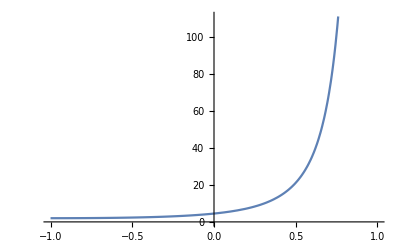

-1/2 (1+2/(-1+c))^2 (-1-c)-8/(-1+c)^3-((1+2/(-1+c)) (-1-c)^2)/(-1+c)^2+1/2 (-1+c)

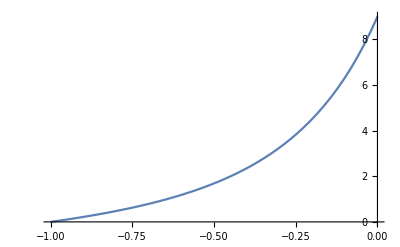

```mathematica
(* units where s = 1 *)
u = -(1 + c)/2;
t = -(1 - c)/2;
u^2(1 + 1/t)^2 + t^2 + t^-2 /. c->-1
Plot[u^2(1 + 1/t)^2 + t^2 + t^-2, {c, -1, 1}]
D[u^2(1 + 1/t)^2 + t^2 + t^-2, c]
Plot[%, {c, -1, 0}]
```

```mathematica
(γ[0] + γ[1]).γ[2] // MatrixForm
```

(-ⅈ | ⅈ | 0 | 0
-ⅈ | ⅈ | 0 | 0
0 | 0 | -ⅈ | -ⅈ
0 | 0 | ⅈ | ⅈ)

```mathematica
{p0, p1, p2, p3}.γs.{0, 1, 0, 0} // MatrixForm
```

(0
0
-p1+ⅈ p2
p0+p3)

```mathematica
((p1 + ⅈ*p2)(k0 + k3)^(1/2)(p0 + p3)^(-1/2) - (k1 + ⅈ*k2)(p0 + p3)^(1/2)(k0 + k3)^(-1/2))
((k0+k3) (p1+ⅈ p2)-(k1+ⅈ k2) (p0+p3))/(√(k0+k3) √(p0+p3))*((k0+k3) (p1-ⅈ p2)-(k1-ⅈ k2) (p0+p3))/(√(k0+k3) √(p0+p3)) // Expand
```

(√(k0+k3) (p1+ⅈ p2))/(√(p0+p3))-((k1+ⅈ k2) √(p0+p3))/(√(k0+k3))

(k1^2 p0^2)/((k0+k3) (p0+p3))+(k2^2 p0^2)/((k0+k3) (p0+p3))-(2 k0 k1 p0 p1)/((k0+k3) (p0+p3))-(2 k1 k3 p0 p1)/((k0+k3) (p0+p3))+(k0^2 p1^2)/((k0+k3) (p0+p3))+(2 k0 k3 p1^2)/((k0+k3) (p0+p3))+(k3^2 p1^2)/((k0+k3) (p0+p3))-(2 k0 k2 p0 p2)/((k0+k3) (p0+p3))-(2 k2 k3 p0 p2)/((k0+k3) (p0+p3))+(k0^2 p2^2)/((k0+k3) (p0+p3))+(2 k0 k3 p2^2)/((k0+k3) (p0+p3))+(k3^2 p2^2)/((k0+k3) (p0+p3))+(2 k1^2 p0 p3)/((k0+k3) (p0+p3))+(2 k2^2 p0 p3)/((k0+k3) (p0+p3))-(2 k0 k1 p1 p3)/((k0+k3) (p0+p3))-(2 k1 k3 p1 p3)/((k0+k3) (p0+p3))-(2 k0 k2 p2 p3)/((k0+k3) (p0+p3))-(2 k2 k3 p2 p3)/((k0+k3) (p0+p3))+(k1^2 p3^2)/((k0+k3) (p0+p3))+(k2^2 p3^2)/((k0+k3) (p0+p3))

```mathematica
((k0+k3)^2 p1^2-2 k1 (k0+k3) p1 (p0+p3)+k1^2 (p0+p3)^2+((k0+k3) p2-k2 (p0+p3))^2)/((k0+k3) (p0+p3))/. {k0->10, k1->0, k2->10, k3->0, p0->10, p1->0, p2->0, p3->10}
```

200